```mathematica
(*---Part 1:Visualizing the Normal and Log-Normal Distributions---*)(*Define the parameters for our underlying normal distribution*)(*mu is the mean,sigma is the standard deviation*)Manipulate[(*The entire block of code will re-run when you move a slider*)Module[{normalDist,logNormalDist,plot1,plot2},(*Create the distributions based on the dynamic slider values*)normalDist=NormalDistribution[mu,sigma];
logNormalDist=LogNormalDistribution[mu,sigma];
(*Plot 1:Normal Distribution*)plot1=Plot[PDF[normalDist,x],{x,-8,8},(*Wider range to see the effect of changing mu*)PlotRange->{{-8,8},{0,2.5}},(*Fixed plot range for stability*)PlotStyle->Directive[Blue,Thick],Filling->{1->{Axis,LightBlue}},PlotLegends->{"Normal Distribution"},GridLines->Automatic,AxesLabel->{"Value","Probability Density"},PlotLabel->"Normal Distribution",ImageSize->500 (*Ensures a good plot size*)];
(*Plot 2:Log-Normal Distribution*)plot2=Plot[PDF[logNormalDist,x],{x,0,8},(*Wider range*)PlotRange->{{0,8},{0,2.5}},(*Fixed plot range for stability*)PlotStyle->Directive[Red,Thick],Filling->{1->{Axis,LightRed}},PlotLegends->{"Log-Normal Distribution"},GridLines->Automatic,AxesLabel->{"Value","Probability Density"},PlotLabel->"Log-Normal Distribution",ImageSize->500 (*Ensures a good plot size*)];
(*Display the plots stacked vertically*)Column[{plot1,plot2}]],(*---Slider Definitions---*)(*Slider for mu (mean),starts at 0,ranges from-2 to 2*){{mu,0,"Mean (μ)"},-2,2,Appearance->"Labeled"},(*Slider for sigma (std dev),starts at 1,ranges from 0.1 to 3*){{sigma,1,"Std Dev (σ)"},0.1,3,Appearance->"Labeled"}]
AreaNormal=Integrate[PDF[normalDist,x],{x,-Infinity,Infinity}];
AreaLogNormal = Integrate[PDF[logNormalDist,x], {x,-Infinity,Infinity}];
```

```mathematica
sigma=1;
mu=0;
(*Create the distributions*)
normalDist=NormalDistribution[mu,sigma];
logNormalDist=LogNormalDistribution[mu,sigma];

plot1=Plot[PDF[normalDist,x],{x,-4,4},(*Adjusted range for better view of normal dist*)PlotRange->All,PlotStyle->Directive[Blue,Thick],Filling->{1->{Axis,LightBlue}},PlotLegends->{"Normal Distribution"},GridLines->Automatic,AxesLabel->{"Value","Probability Density"},PlotLabel->"Normal Distribution"]
(*Plot 2:Log-Normal Distribution*)
plot2=Plot[PDF[logNormalDist,x],{x,0,5},(*Adjusted range for better view of log-normal dist*)PlotRange->All,PlotStyle->Directive[Red,Thick],Filling->{1->{Axis,LightRed}},PlotLegends->{"Log-Normal Distribution"},GridLines->Automatic,AxesLabel->{"Value","Probability Density"},PlotLabel->"Log-Normal Distribution"]
```

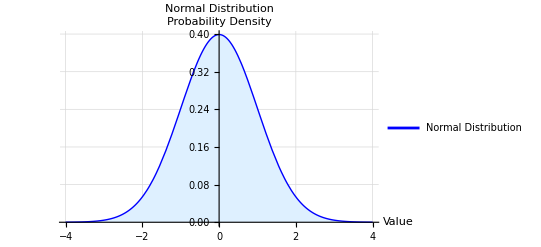

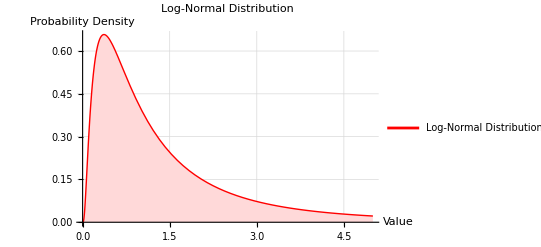

-Graphics-

Calculated d2: -0.0939508

Probability of finishing in-the-money (N(d2)): 0.462574

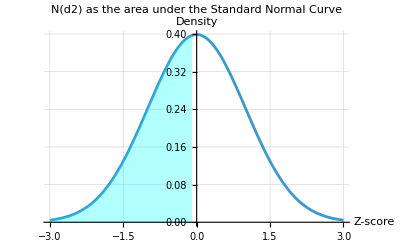
{{-Graphics-},{□}}

```mathematica
randomNormalData=RandomVariate[normalDist,100000];
(*Transform this data by taking the exponential of each point*)
randomLogNormalData=Exp[randomNormalData];
(*Create histograms of both datasets to show how the transformation works*)
GraphicsRow[{Histogram[randomNormalData,Automatic,"PDF",ChartStyle->LightBlue,ChartLegends->{"Normally Distributed Data"},AxesLabel->{"Value","Density"}],Histogram[randomLogNormalData,Automatic,"PDF",ChartStyle->LightRed,ChartLegends->{"Exponentiated (Log-Normal) Data"},AxesLabel->{"Value","Density"}]},ImageSize->Large,Spacings->10]
```

```mathematica
(*---Black-Scholes Option Pricing*)(*Define the parameters for the European call*)
(*Define the parameters for the European call option*)
s=100.0;  (*Underlying*)
k=110.0;  (*Strike*)
r=0.05;   (*Risk-Free  Rate*)
sigma=0.40; (*Vol*)
t=.25;   (*Time to Maturity in years (3 months)*)

(*Calculate the option price and its Greeks using the built-in FinancialDerivative function.This version uses the explicit,named-parameter syntax which is clearer and less error-prone.*)
optionAnalytics=FinancialDerivative[{"European","Call"},(*Type of derivative*){"StrikePrice"->k,"Expiration"->t},(*Derivative-specific parameters*){"InterestRate"->r,"Volatility"->sigma,"CurrentPrice"->s},(*Market parameters*){"Value","Greeks"}        (*Properties to calculate*)];
f[x_]:=CDF[NormalDistribution[0,1],x]

(*Calculate d1 and d2 from the Black-Scholes formula*)
d1=(Log[s/k]+(r+sigma^2/2)*t)/(sigma*Sqrt[t]);
d2=d1-sigma*Sqrt[t];

(*Calculate the final call option price using the BSM formula:C=S*N(d1)-K*e^(-rt)*N(d2)*)
deltaOption = f[d1]
callPrice=s*f[d1]-k*Exp[-r*t]*f[d2]
callPrice == optionAnalytics[[1]] (*are the prices samme*)
optionAnalytics
```

0.376741

4.69208

True

{4.69208,{Delta→0.376743,Gamma→0.0189874,Rho→8.24555,Theta→-16.839,Vega→18.9875}}